```mathematica
L[x_,r_]=4 r x(1-x)
Logistic[x0_,n_,r_]:=NestList[L[#,r]&,x0,n]
DF[x_,r_]=D[L[x,r],x]
LYALogistic[list_,r_]:=1/Length[list]  Total[Log[Abs[DF[#,r]]]&/@list]
```

4 r (1-x) x

4 r (1-x)-4 r x

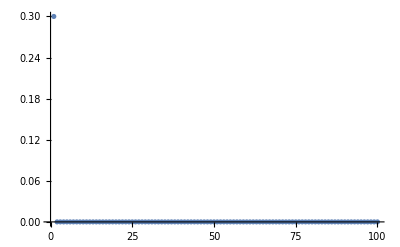
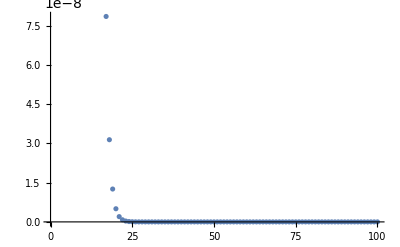
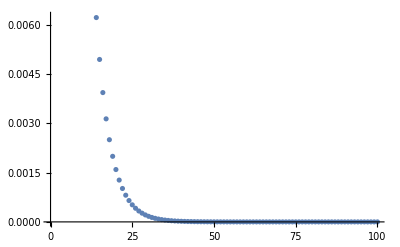
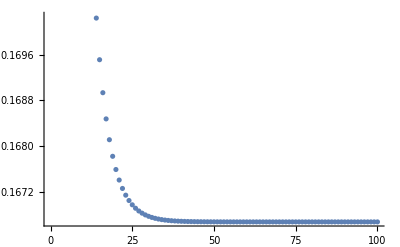
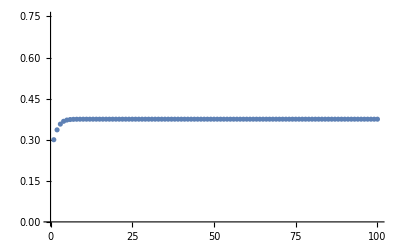
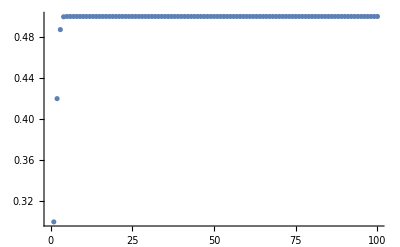
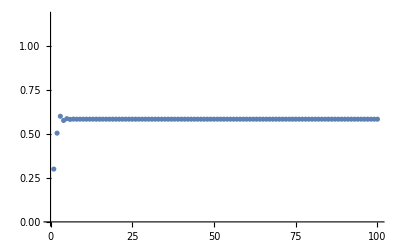
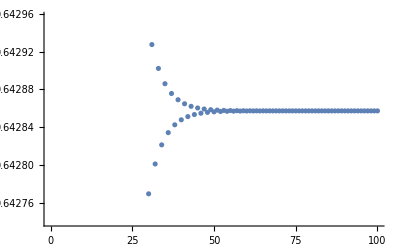

-Graphics-

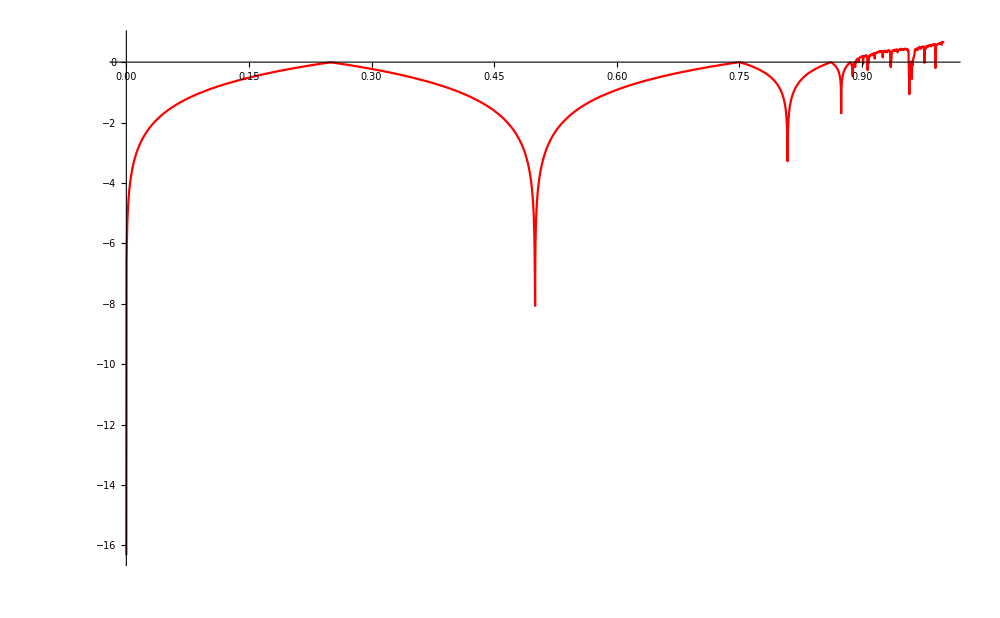

-Graphics-

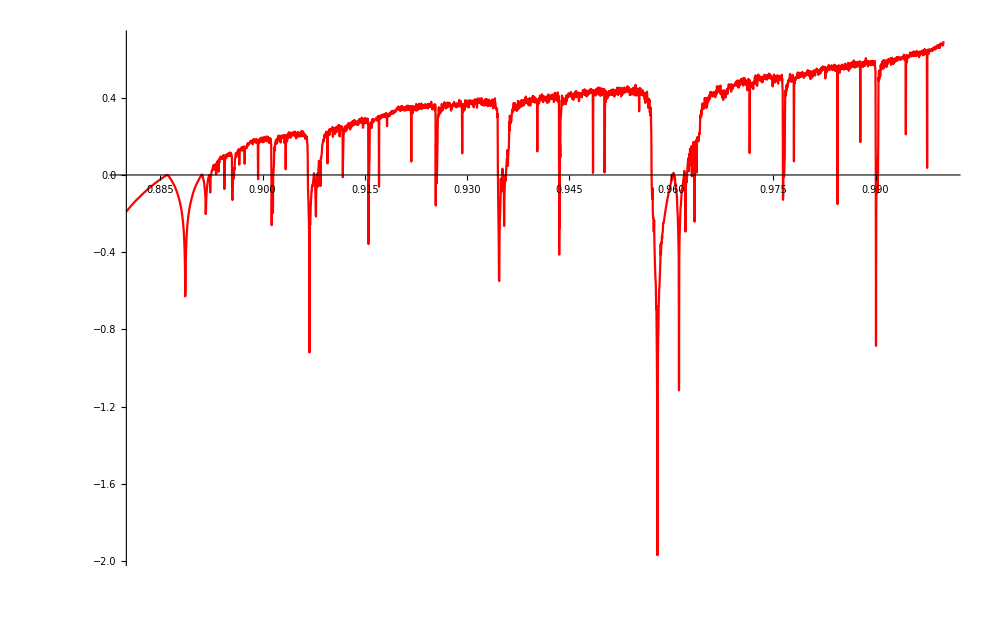

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
eachDomain=Range[0,1,.1];
points=Logistic[.3, 10000, #]&/@eachDomain;
ListPlot[ #[[1;;100]] ]&/@points
(*Histogram[#]&/@points*)
Histogram[#,{0,1,.05}]&/@points

BifurcationDiagram[r1_:0,r2_:1,iterations_:1000,resolution_:1000]:=(Module[{rs},
rs=Range[r1,r2,(r2-r1)/resolution];
ListPlot[
Flatten[
Partition[
Riffle[
Logistic[0.5,iterations,#],
#][[100;;iterations]],
2]&/@rs
,1]
,ImageSize->1000,PlotStyle->{Directive[PointSize[.000000001],Opacity[.05]]}]
])
LyapunovPlot[r1_:0,r2_:1,iterations_:1000]:=Plot[LYALogistic[Logistic[0.3,iterations,r],r],{r,r1,r2},ImageSize->1000,PlotStyle->Red,PlotRange->Full]
BifurcationDiagram[]
LyapunovPlot[]
BifurcationDiagram[0.88]
LyapunovPlot[.88]
```

```mathematica
p
```

p